# Data preprocessing for complex Wilson network

## 1410.2546

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

## 1607.04049

Data columns are:
“T [GeV]”
“r [fm]”
“Re[V] [GeV]” or “Im[V] [GeV]”
“Err[Re[V]] [GeV]” or “Err[Im[V]] [GeV]” this is the ten-bin Jackknife error
“Err[Re[V]] [GeV]” or “Err[Im[V]] [GeV]” this is the “systematic errors”

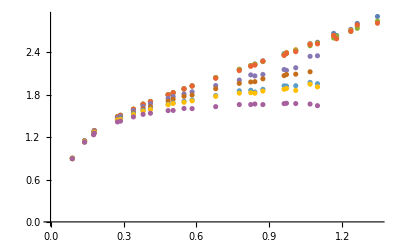

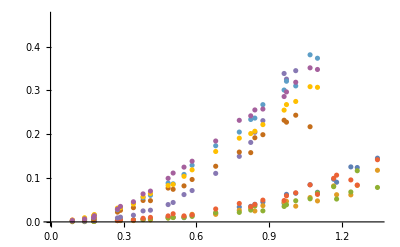

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

Find the available temperatures.

```mathematica
temps=First/@dataRe//Union;
temps==Union[First/@dataIm]
```

True

Convert the data for each temperature to its own file in the correct format.

The target files have rows: “T r [1]”, “Re[V]/T [1]”, “Err[Re[V]]/T [1]”, “Im[V]/T [1]”, “Err[Im[V]]/T [1]”
Note: we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

```mathematica
temps
```

{0.112778,0.225556,0.25375,0.270667,0.29,0.312308,0.338333,0.369091,0.406}

```mathematica
GetData[T_]/;MemberQ[temps,T]:=Block[{r,ReV,ReVσ,ImV,ImVσ,re,im},
re=Rest/@Select[dataRe,First[#]==T&];
im=Rest/@Select[dataIm,First[#]==T&];
Check[re⟦;;,1⟧==im⟦;;,1⟧,"Inconsistent widths in Re and Im files."];
r=re⟦;;,1⟧;
ReV=re⟦;;,2⟧;
ReVσ=re⟦;;,3⟧;
ImV=im⟦;;,2⟧;
ImVσ=im⟦;;,3⟧;
{T fmToInvGeV[r],ReV/T,ReVσ/T,-ImV/T,ImVσ/T}
]
```

T = 113 MeV

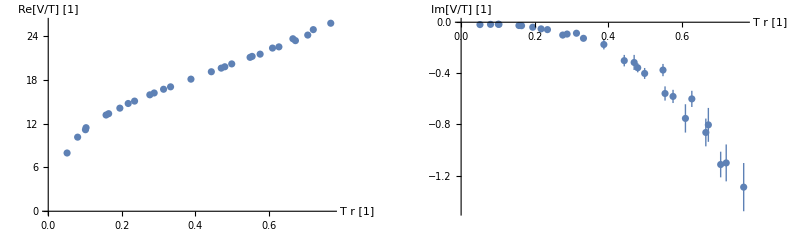

T = 226 MeV

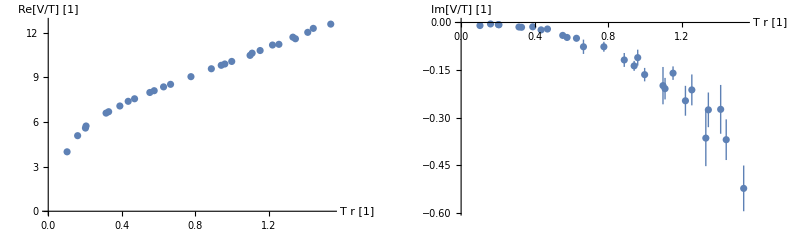

T = 254 MeV

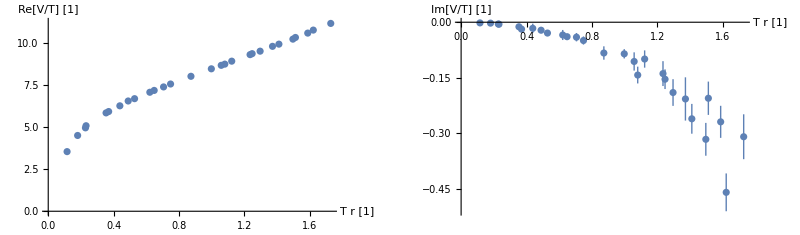

T = 271 MeV

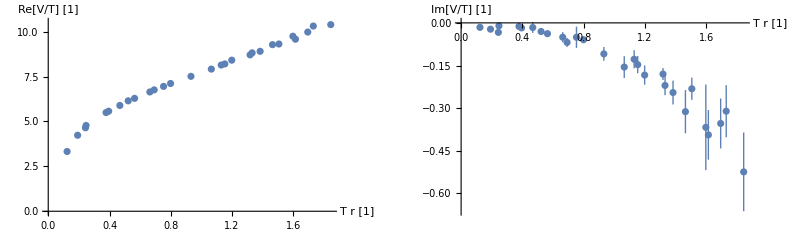

T = 290 MeV

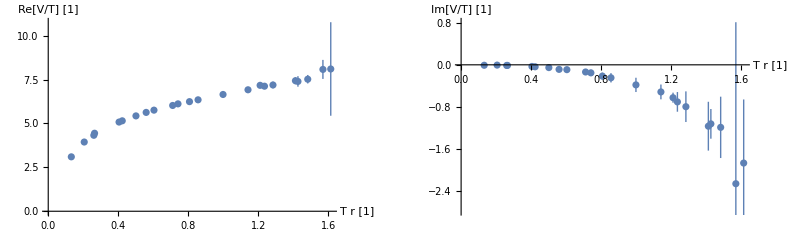

T = 312 MeV

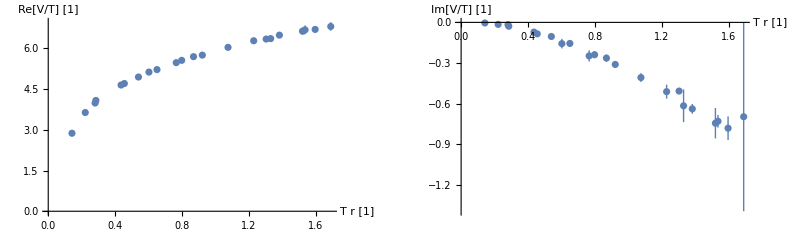

T = 338 MeV

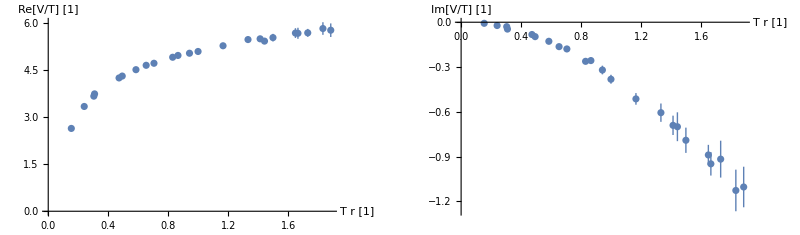

T = 369 MeV

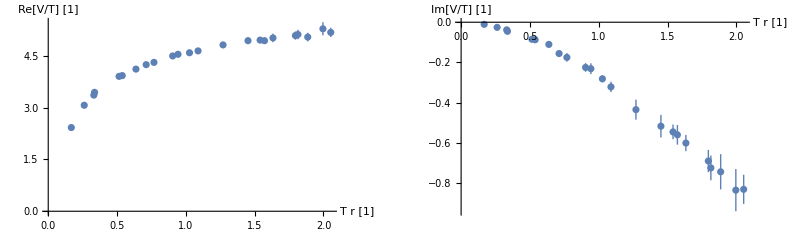

T = 406 MeV

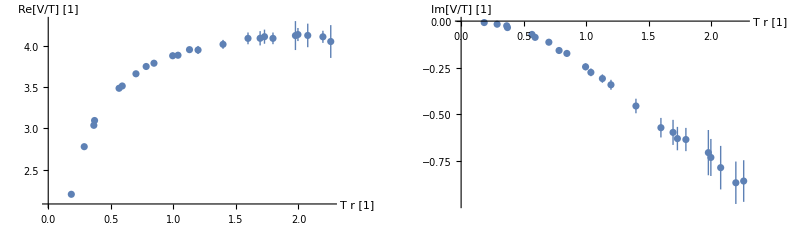

```mathematica
Block[{r,ReV,ReVσ,ImV,ImVσ,re,im},
Do[
{r,ReV,ReVσ,ImV,ImVσ}=GetData[T];
Print["T = "<>ToString[Round[1000T]]<>" MeV"];
GraphicsRow[{ListPlot[Thread@{r,Around@@@Thread[{ReV,ReVσ}]},AxesLabel->{"T r [1]","Re[V/T] [1]"}],ListPlot[Thread@{r,Around@@@Thread[{ImV,ImVσ}]},AxesLabel->{"T r [1]","Im[V/T] [1]"}]}]//Print;
Export[NotebookDirectory[]<>"data/preprocessed/1607.04049/"<>ToString[Round[1000T]]<>"MeV.txt",{T fmToInvGeV[r],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"],
{T,temps}
]
]
```

Note that these plot don’t have the manual shifts that Fig. 2 has.

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

## Fitting scaling laws to IR-data

### Power laws

This system has a deconfinement temperature T_c=290 MeV, so there are 4 temperatures above that. This data has to be shifted so that Re[V/T] goes to zero asymptotically, so we make a hypothesis
Re[V/T]=a/(T r)^b+V_∞ ,
for a<0 and b>0. The parameter V_∞ is intended to shift Re[V/T] to zero asymptotically.

```mathematica
FitPowerLawReal[T_]:=Block[{r=GetData[T]⟦1⟧,ReV=GetData[T]⟦2⟧,fit},
fit=FindFit[Thread[{r,ReV}],a/x^b+V∞,{a,b,V∞},x];
Print["fit = ",a/x^b+V∞/.fit];
GraphicsRow[{Show[Plot[a/x^b/.fit,{x,0.1,2.2},PlotRange->All,AxesLabel->{"T r","Re[V]/T"}],ListPlot[Thread[{r,ReV-V∞/.fit}],PlotStyle->Black]],Show[LogLogPlot[-a/x^b/.fit,{x,0.1,2.2},AxesLabel->{"T r","-Re[V]/T"}],ListLogLogPlot[Thread[{r,-ReV+V∞/.fit}],PlotStyle->Black]]}]
]
```

```mathematica
temps
```

{0.112778,0.225556,0.25375,0.270667,0.29,0.312308,0.338333,0.369091,0.406}

T = 312 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = 350.682-344.74/x^0.00451198

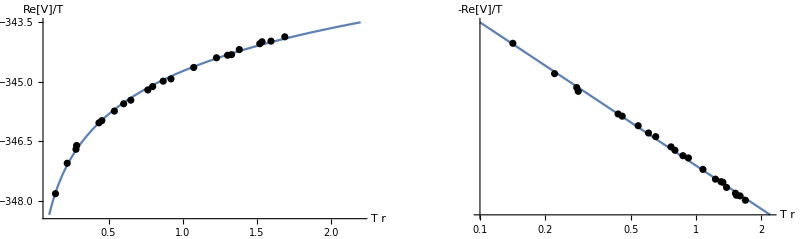

```mathematica
With[{T=temps⟦6⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawReal[T]]
```

T = 338 MeV

fit = 10.8966-5.75868/x^0.190206

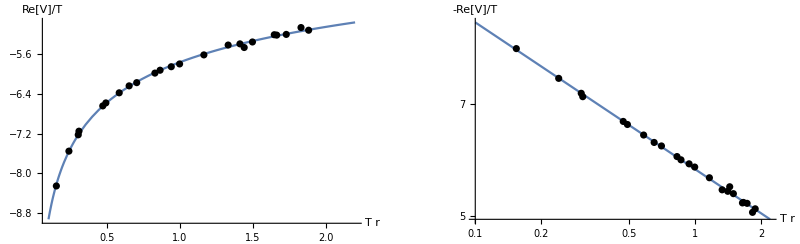

```mathematica
With[{T=temps⟦7⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawReal[T]]
```

T = 369 MeV

fit = 8.14933-3.57062/x^0.263379

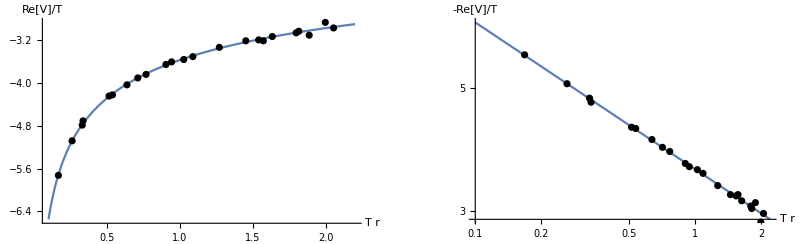

```mathematica
With[{T=temps⟦8⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawReal[T]]
```

T = 406 MeV

fit = 4.53547-0.682127/x^0.739602

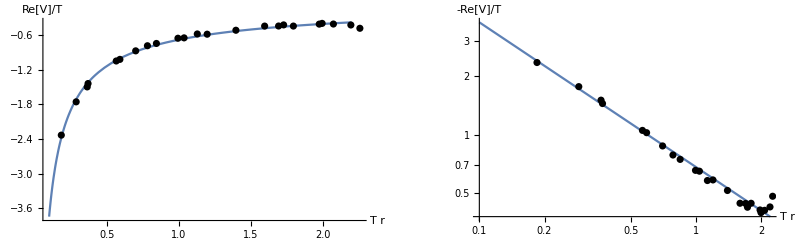

```mathematica
With[{T=temps⟦9⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawReal[T]]
```

```mathematica
GetData[temps⟦-1⟧]
```

{{0.184544,0.287774,0.364461,0.370316,0.566112,0.591477,0.701152,0.78278,0.84513,0.99464,1.03709,1.12904,1.19753,1.39712,1.5967,1.69356,1.72848,1.79629,1.97582,1.99588,2.07418,2.19547,2.25808},{2.20131,2.77802,3.03671,3.09494,3.48537,3.51317,3.66093,3.74935,3.78885,3.87923,3.88565,3.95326,3.94918,4.01763,4.08985,4.09097,4.11025,4.09001,4.12374,4.13642,4.12539,4.10875,4.05165},{0.000566726,0.00490484,0.0056919,0.00594008,0.0134078,0.0191913,0.0084626,0.0244312,0.0191094,0.0377611,0.0155957,0.0308927,0.0488316,0.0539181,0.0712993,0.0864813,0.0855982,0.0707089,0.175282,0.0791567,0.14273,0.073422,0.198583},{-0.00777232,-0.0165637,-0.0251907,-0.0346714,-0.0713899,-0.0870793,-0.11309,-0.157459,-0.173179,-0.244928,-0.27468,-0.307816,-0.341155,-0.454781,-0.57102,-0.59616,-0.629383,-0.634372,-0.70462,-0.730534,-0.785127,-0.86603,-0.856841},{0.00111712,0.00277431,0.004288,0.00526717,0.00399493,0.00852489,0.00930798,0.0142022,0.0121989,0.0184455,0.0205224,0.0223737,0.0266857,0.0390119,0.0523324,0.0671364,0.0626953,0.0622485,0.121177,0.0991409,0.116554,0.11362,0.111457}}

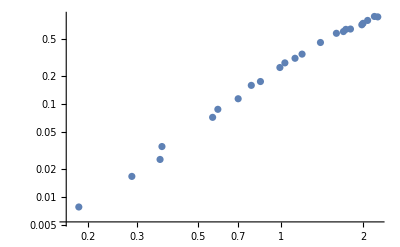

{a→0.281398,b→1.35318,c→0.0228566}

```mathematica
ListLogLogPlot@Thread[{%97⟦1⟧,-%97⟦4⟧}]
FindFit[Thread[{%97⟦1⟧,-%97⟦4⟧}]⟦-10;;⟧,{a x^b+c},{a,b,c},x]
```

```mathematica
FitPowerLawImag[T_]:=Block[{r=GetData[T]⟦1⟧,ImV=GetData[T]⟦4⟧,fit},
fit=FindFit[Thread[{r,ImV}]⟦-10;;⟧,a x^b+c,{a,b,c},x];
Print["fit = ",a x^b+c/.fit];
GraphicsRow[{Show[Plot[a x^b/.fit,{x,0.1,2.2},PlotRange->All,AxesLabel->{"T r","Im[V]/T"}],ListPlot[Thread[{r,ImV-c/.fit}],PlotStyle->Black]],Show[LogLogPlot[-a x^b/.fit,{x,0.1,2.2},AxesLabel->{"T r","-Im[V]/T"}],ListLogLogPlot[Thread[{r,-ImV+c/.fit}],PlotStyle->Black]]}]
]
```

T = 312 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = 30.7229-31.0854 x^0.0253935

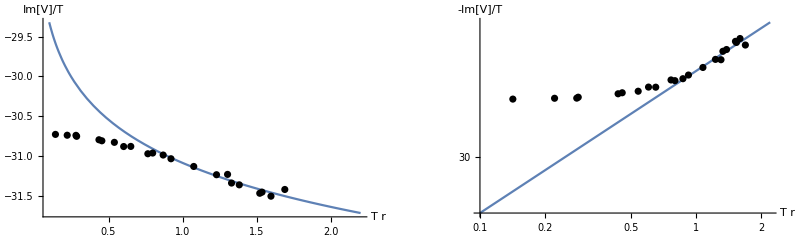

```mathematica
With[{T=temps⟦6⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawImag[T]]
```

T = 338 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = -55.6546+55.4019/x^0.0240778

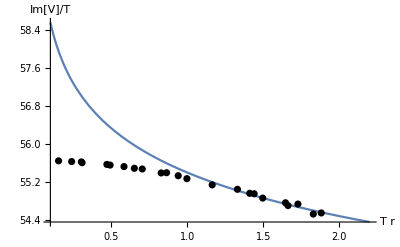

```mathematica
With[{T=temps⟦7⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawImag[T]]
```

T = 369 MeV

fit = -0.145809-0.18108 x^1.89354

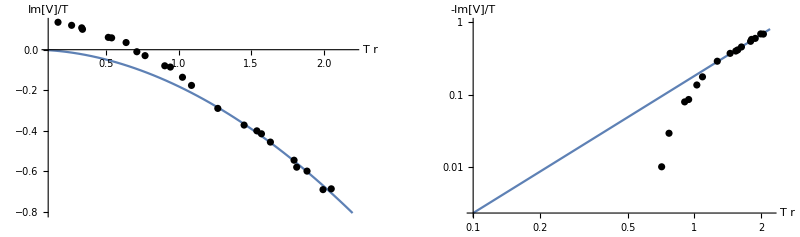

```mathematica
With[{T=temps⟦8⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawImag[T]]
```

T = 406 MeV

fit = -0.0228566-0.281398 x^1.35318

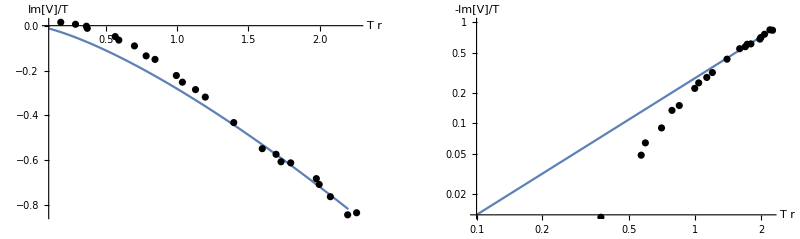

```mathematica
With[{T=temps⟦9⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitPowerLawImag[T]]
```

### Exponential behavior

This time we want to fit a “Debye screening” version
Re[V/T]=a/r ⅇ^(-b (T r))+V_∞ .

```mathematica
FitExponential[T_]:=Block[{r=GetData[T]⟦1⟧,ReV=GetData[T]⟦2⟧,fit},
fit=FindFit[Thread[{r,ReV}],a Exp[-b x]+V∞,{a,b,V∞},x];
Print["fit = ",a Exp[-b x]/x+V∞/.fit];
GraphicsRow[{Show[Plot[a Exp[-b x]/.fit,{x,0.1,2.2},PlotRange->All,AxesLabel->{"T r","Re[V]/T"}],ListPlot[Thread[{r,ReV-V∞/.fit}],PlotStyle->Black]],Show[LogLogPlot[-a Exp[-b x]/.fit,{x,0.1,2.2},AxesLabel->{"T r","-Re[V]/T"}],ListLogLogPlot[Thread[{r,-ReV+V∞/.fit}],PlotStyle->Black]]}]
]
```

T = 312 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = -759.33+(762.869 ⅇ^(0.00280687 x))/x

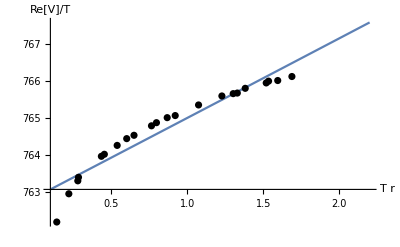

```mathematica
With[{T=temps⟦6⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitExponential[T]]
```

T = 338 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = -679.661+(683.072 ⅇ^(0.00211078 x))/x

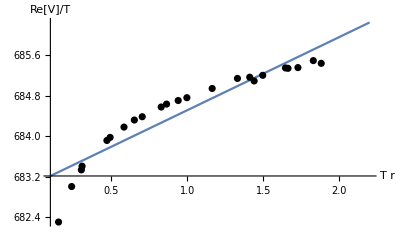

```mathematica
With[{T=temps⟦7⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitExponential[T]]
```

T = 369 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = -701.66+(704.811 ⅇ^(0.00162288 x))/x

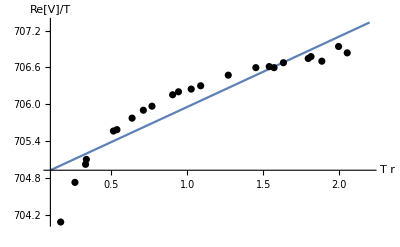

```mathematica
With[{T=temps⟦8⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitExponential[T]]
```

T = 406 MeV

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

fit = -628.993+(631.964 ⅇ^(0.00100075 x))/x

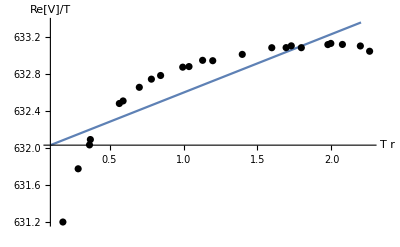

```mathematica
With[{T=temps⟦9⟧},Print["T = "<>ToString[Round[1000T]]<>" MeV"];FitExponential[T]]
```